```mathematica
data = Import["/net/home/f09/bajennissen/research/DAY187/sec_int_data/675nm.dat"]
```

{{1.45287,0.173365},{1.39708,0.0973989},{1.35876,0.041046},{1.32403,0.00955421},{1.28662,-0.0319139},{1.25869,-0.0440564},{1.22636,-0.0523676},{1.19613,-0.0480984},{1.17366,-0.06145},{1.15413,-0.0989147},{1.12528,-0.14922},{1.11495,-0.0693822},{1.10625,-0.0611204},{1.09912,-0.0428762},{1.09306,-0.00511305},{1.0888,0.0165621},{1.08648,-0.0051231},{1.08572,-0.0230639},{1.08632,-0.117062},{1.0888,-0.139963},{1.09505,-0.0183371},{1.09559,-0.00047011},{1.12528,0.0613773},{1.14263,0.115291},{1.16354,0.149626},{1.19414,0.180737},{1.22405,0.192354},{1.25343,0.206201},{1.28081,0.200325},{1.31748,0.208963},{1.36987,0.21018},{1.42194,0.209694},{1.47153,0.195731},{1.11308,0.0684994}}

-0.68636+0.601502 x

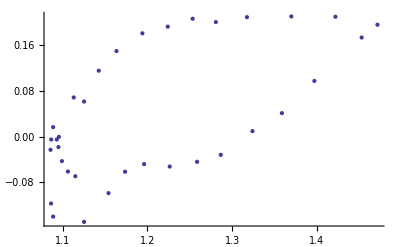

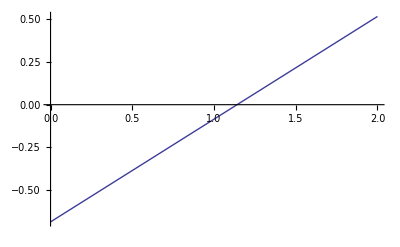

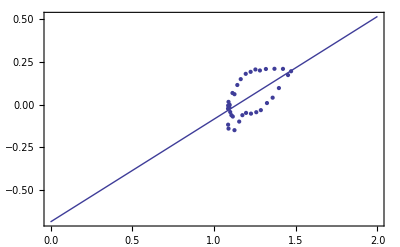

```mathematica
line = Fit[data,{1,x},x]
DataPlot=ListPlot[data]
FitPlot=Plot[line,{x,0,2}]
Show[DataPlot,FitPlot,PlotRange->All,Frame->True,AxesOrigin->{0,0}]
```